## LSTM

```mathematica
loadTimeSeriesResampled=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\LoadtimeseriesResampled.wxf"];
```

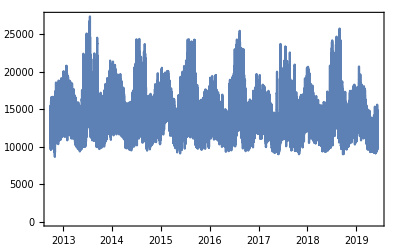

```mathematica
DateListPlot[loadTimeSeriesResampled]
```

```mathematica
data=loadTimeSeriesResampled//Normal;
```

```mathematica
values=QuantityMagnitude@data[[All,2]];keysp=Partition[values,10,1];valuesp = values[[10;;]];
```

```mathematica
threaddata=Thread[Table[ArrayReshape[keysp[[i]],{1,10}]->valuesp[[i]],{i,1,Length@valuesp}]];
```

```mathematica
Length@data
```

58680

```mathematica
58680
```

```mathematica
Length@threaddata
```

57680

```mathematica
trainingdata[[;;1]]
```

{{{11641.4,10883.1,10707.6,10663.2,10627.7,10848.8,11520.7,12877.6,14087.2,14646.6}}→14646.6}

```mathematica
mldata=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\mldata.wxf"];
```

```mathematica
templag24load=AssociationThread[{"Temperature","Lag24", "Load"} -> Transpose@mldata[[All, {2, -8,-1}]]]
```

<|Temperature→{13.3008,13.3,13.3,13.2994,13.3,12.8003,12.2004,12.2,12.2,12.7996,12.8,58629,20.5999,20.,20.5999,20.,20.,21.7,21.7,21.1,21.7,21.7},1,Load→1|>
 |  |  |  |

```mathematica
templag24load[[1]]
```

{13.3008,13.3,13.3,13.2994,13.3,12.8003,12.2004,12.2,12.2,12.7996,12.8,13.2993,58626,20.,21.0999,20.5999,20.,20.5999,20.,20.,21.7,21.7,21.1,21.7,21.7}
 |  |  |  |

```mathematica
shortExample=Map[Take[#,15]&,templag24load]
```

<|Temperature→{13.3008,13.3,13.3,13.2994,13.3,12.8003,12.2004,12.2,12.2,12.7996,12.8,13.2993,13.3,13.3,13.8996},Lag24→{11520.7,12877.6,14087.2,14646.6,14992.9,15267.5,15400.2,15361.9,15344.1,15176.5,15081.6,15134.4,15283.5,15510.1,15443.3},Load→{10605.9,10775.7,11856.2,12979.6,13753.7,13870.1,13955.2,13865.3,13643.7,13457.9,13354.2,13466.1,13773.,14224.4,14401.8}|>

```mathematica
Length/@shortExample
```

<|Temperature→15,Lag24→15,Load→15|>

```mathematica
temp=templag24load[[1,All]];
lag24=templag24load[[2,All]];
load=templag24load[[3,All]];
```

```mathematica
tempp=Partition[temp,12,1];
```

```mathematica
Length@tempp
```

58639

```mathematica
58640-12
```

58628

```mathematica
tempp=Partition[temp,12,1];lag24p=Partition[lag24,12,1];loadp=Partition[lag24,12,1];
```

```mathematica
inputtable=Thread[Table[Transpose@{tempp[[i]],lag24p[[i]],loadp[[i]]},{i,1,500}]-> Table[load[[i+12]],{i,1,500}]]
```

{{{13.3008,11520.7,11520.7},{13.3,12877.6,12877.6},{13.3,14087.2,14087.2},{13.2994,14646.6,14646.6},{13.3,14992.9,14992.9},{12.8003,15267.5,15267.5},{12.2004,15400.2,15400.2},{12.2,15361.9,15361.9},{12.2,15344.1,15344.1},{12.7996,15176.5,15176.5},{12.8,15081.6,15081.6},{13.2993,15134.4,15134.4}}→13773.,498,{{18.9025,10953.1,10953.1},{18.9,10887.,10887.},9,{17.7939,15503.7,15503.7}}→14042.3}
 |  |  |  |

```mathematica
trainingdata[[1,2]]
```

13773.

```mathematica
{trainingdata,testdata}=TakeDrop[inputtable,45]
```

{{{{13.3008,11520.7,11520.7},{13.3,12877.6,12877.6},{13.3,14087.2,14087.2},6,{12.7996,15176.5,15176.5},{12.8,15081.6,15081.6},{13.2993,15134.4,15134.4}}→13773.,43,{1}→15082.9},{1}}
 |  |  |  |

```mathematica
trainingdata[[1;;]]
```

{{13.3008,11520.7,11520.7},{13.3,12877.6,12877.6},{13.3,14087.2,14087.2},{13.2994,14646.6,14646.6},{13.3,14992.9,14992.9},{12.8003,15267.5,15267.5},{12.2004,15400.2,15400.2},{12.2,15361.9,15361.9},{12.2,15344.1,15344.1},{12.7996,15176.5,15176.5},{12.8,15081.6,15081.6},{13.2993,15134.4,15134.4}}→13773.

```mathematica
testdata
```

{{{12.7881,9829.64,9829.64},{6.73743,9658.6,9658.6},{21.3269,9648.07,9648.07},{10.6007,9814.86,9814.86},{10.6,10056.5,10056.5},{10.6,10711.6,10711.6},{10.0009,11761.4,11761.4},{10.5992,12717.6,12717.6},{11.0993,13316.6,13316.6},{13.2965,13648.9,13648.9},{14.9975,13783.5,13783.5},{16.6975,13686.4,13686.4}}→14995.6,453,{{18.9025,10953.1,10953.1},10,{17.7939,15503.7,15503.7}}→9}
 |  |  |  |

```mathematica
{{seq1},{seq2},{seq3}}-> value3+1
```

```mathematica
{{value1},{value2},{value3}}-> value3
```

```mathematica
net[]
```

```mathematica
net[<|"input1"-> ...,|>]
```

```mathematica
NetGraph[<|elements(layers, graph, chain)|>,{edges, elemi-> elemj, NetPort[elemi, portname]-> ...}, "Input" -> (dimensions/NetEncoder[]/NetDecoder[])]
```

```mathematica
columnHeads=v/@{"timeStep","temperature","BusinessDay","Lag1","Lag2","Lag3","Lag4","Lag5","Lag6","Lag7","Lag8","Lag9","Lag10","Lag11","Lag12","Lag13","Lag14","Lag15","Lag16","Lag17","Lag18","Lag19","Lag20","Lag21","Lag22","Lag23","Lag24","Lag25","Lag26","Lag27","Lag28","Lag29","Lag30","Load"}
```

{v[timeStep],v[temperature],v[BusinessDay],v[Lag1],v[Lag2],v[Lag3],v[Lag4],v[Lag5],v[Lag6],v[Lag7],v[Lag8],v[Lag9],v[Lag10],v[Lag11],v[Lag12],v[Lag13],v[Lag14],v[Lag15],v[Lag16],v[Lag17],v[Lag18],v[Lag19],v[Lag20],v[Lag21],v[Lag22],v[Lag23],v[Lag24],v[Lag25],v[Lag26],v[Lag27],v[Lag28],v[Lag29],v[Lag30],v[Load]}

```mathematica
rnn=NetChain[{
	LongShortTermMemoryLayer[20],
	NetMapOperator[NetChain[{
	LinearLayer[100],
	ElementwiseLayer[Ramp],
	60,
	Ramp,
	50,
	Ramp,1}]
],SequenceLastLayer[]}, "Input"-> {"Varying",3}]
```

NetChain[<>]

```mathematica
NetInitialize[rnn][Transpose[Values[shortExample]]]
```

{{0.345405},{0.404694},{0.413519},{0.414735},{0.4149},{0.414922},{0.414925},{0.414926},{0.414926},{0.414926},{0.414926},{0.414926},{0.414926},{0.414926},{0.414926}}

```mathematica
NetInitialize[rnn][<|"Input"-> Transpose[Values[templag24load]] |>]
```

{{0.251166},{0.40458},{0.422853},{0.512209},{0.308946},{0.308965},{0.308967},{0.308967},{0.512545},{0.512545},{0.512545},{0.512545},{0.308967},{0.308967},58622,{0.437191},{0.437191},{0.437191},{0.437191},{0.437191},{0.437191},{0.437191},{0.437191},{0.442665},{0.442665},{0.442665},{0.442665},{0.442665},{0.442665}}
 |  |  |  |

```mathematica
trainednet=NetTrain[rnn,inputtable,All,ValidationSet->testdata,BatchSize->800,Method-> "ADAM",MaxTrainingRounds->100]
```

NetTrain::invindim3: Data provided to port "Output" should be a non-empty list of length-1 vectors of real numbers, but was a length-500 vector of real numbers.

$Failed

```mathematica
AssociationMap[ PredictorMeasurements[
Predict[trainingdata,Method->#,PerformanceGoal->"DirectTraining"],testdata, "MeanSquare"]&,{"RandomForest"}]
```

<|RandomForest→279504.|>

```mathematica
SeedRandom[111];rsample=RandomSample[testdata,2]
```

{{{15571.1,15650.6,15550.,15302.7,15084.7,15006.5,15040.4,15374.6,15861.4,16102.7,16253.8,15728.2,14725.2,13468.8,12628.2,12192.5,11892.3,11734.9,11756.3,11787.6,12538.3,14211.6,15276.5,15579.4,15528.3,15204.2,14817.9,14651.6,14463.1,14221.3,14125.9,14382.,14516.6,14935.4,15450.,15188.9,14329.5,13169.8,12186.3,12101.6,12083.4,12240.9,12305.6,12419.8,13003.6,14180.,14862.8,14680.7,14187.2,13634.8,13336.7,13077.,12740.2,12956.9,13126.7,13239.6,13700.3,14094.1,14587.8,14369.5,13755.3,12871.4,11648.4,11485.9,11075.5,10877.7,10828.,10951.7,11162.2,11860.3,12570.9,13046.8,12917.2,12480.5,12111.6,12008.9,12131.9,12110.4,11984.3,12376.6,12874.8,13339.7,13854.,13696.2,13187.8,12453.8,11907.6,11114.4,10910.2,10951.7,10883.2,10954.5,11021.,11385.1,11920.2,12696.2,13192.6,13334.1,13151.,12902.1,12645.9,12370.8,12374.4,12720.4,13432.5,14122.6,14820.8,14703.8,13927.6,12878.3,12298.3,11565.3,11323.6,11214.8,11304.6,11713.7,12544.7,14395.1,15167.7,14618.8,13866.9,13356.3,12993.1,12918.3,12829.8,12816.8,12604.2,12805.9,13705.3,14536.4,15324.1,15179.2,14307.6,13130.1,12050.8,12007.1,11737.6,11656.4,11731.8,12127.8,12957.,14699.6,15177.3,14624.4,13851.9,13279.5,12894.3,12620.2,12948.8,13164.6,13322.9,13572.6,14213.3,14732.4,15256.6,14902.4,14058.7,12821.8,11565.6,11681.9,11660.6,11488.7,11461.7,11733.1,12227.4,13581.2,14560.9,14592.7,14430.,14046.,13234.9,12632.2,12502.4,12657.9,12760.9,13153.1,13577.4,14003.8,14581.7,14384.3,13546.6,12400.7,11678.1,11149.7,10845.1,10689.9,10957.3,11104.9,11720.8,13249.,14082.1,13914.4,13725.1,13407.9,13084.4,13458.3,13645.3,13338.6,13438.5,13716.8,14075.9,14331.3,14586.3,14210.2,13382.8,12392.,11319.6,10975.3,10567.7,10386.4,10545.2,10761.6,11383.1,12268.9,13007.9,13546.,13795.5,13820.7,13764.4,13627.9,13537.3,13182.3,12969.,13146.5,13481.6,13602.6,13773.3,13482.6,12846.,12009.9,10990.7,10641.9,10242.7,10303.9,10499.5,10427.1,10813.7,11401.3,11566.9,11766.6,11589.8,11264.6,10947.5,10806.6,10783.,10432.7,10721.,10958.7,11626.5,12344.3,13026.2,13078.9,12620.,11880.6,10756.9,10400.6,10344.8,10342.3,10280.,10331.9,10303.7,10488.2,11145.6,11687.6,11897.1,11756.4,11546.3,11316.7,10917.9,10570.7,10538.8,10780.9,10983.4,11724.,12797.8,13073.8,12518.6,11629.9,11838.7,10514.4,10520.2,10417.8,10472.3,10855.6,11987.1,13373.8,14422.6,14907.2,15191.4,15288.,15087.2,14649.9,14213.,13915.8,13853.2,13772.1,13927.4,14518.3,15191.7,15088.3,14184.7,12937.6,12283.6,11396.,11344.9,11229.6,11271.,11422.1,12176.3,13896.1,14684.9,14328.2,13751.,13863.9,14087.2,14252.,14439.5,14386.1,14513.7,14853.7,15362.7,15529.,15567.9,15156.6,14175.6,13113.7,11837.,11377.3,11059.3,10924.1,10903.4,11210.,11760.,13411.3,14477.1,14681.7,14694.4,14672.7,14569.5,14479.3,14827.2,14715.,14612.1,14674.6,14705.4,14668.3,14822.7,14353.1,13883.5,12683.8,12403.9,11253.3,11337.3,11372.9,11690.5,11906.2,12728.3,13999.,14662.,14168.1,13790.7,13722.7,13753.,13473.4,13549.3,13413.6,13460.2,13520.,14010.6,14609.2,15116.8,15158.2,14430.9,13268.1,11746.3,11789.5,11435.3,11313.6,11350.8,11715.4,12514.1,14114.9,14800.,14558.6,14349.9,14359.6,14513.,14736.6,14942.4,14961.1,14887.3,14739.1,14668.6,14573.3,14750.7,14522.8,13786.8,12753.2,11515.,11252.4,10964.5,10811.8,10735.,10838.8,11185.9,11568.6,12359.2,13203.2,13488.1,13062.9,12567.8,12108.9,11993.,11725.6,11485.5,12104.7,12510.,12876.5,13488.8,13539.7,13030.4,12296.2,11777.5,11138.5,10773.6,10614.2,10569.7,10674.4,10985.7,11458.,11887.,12311.9,12401.6,12453.6,12187.4,12041.6,11919.,11805.1,11986.4,12391.1,13095.4,13642.1,14296.7,14256.7,13494.4,12462.9,11626.4,11511.4,11217.3,11153.7,11261.8,11694.9,12401.7,13935.3,14608.4,14190.4,13643.3,13211.8,12936.1,12597.5,12553.8,12304.6,12329.6,12809.9,13499.8,14208.7,14849.,14794.7,13896.4,12672.8,11857.4,10934.9,10616.9,10725.,10737.7,11095.8,11887.7,13521.3,14444.2,14525.6,14458.8,14489.7,14399.9,14193.1,14053.9,13841.,13728.2,13924.2,14348.3,14647.7,15024.6,14968.2,14119.1,12908.5,11636.5,11223.1,11193.4,11121.2,11110.2,11412.8,12330.3,13980.1,14633.3,14109.9,13316.1,12820.4,12601.7,12400.8,12359.3,12592.,12812.2,13184.6,13522.8,13920.5,14485.2,14544.3,13716.5,12527.7,11304.1,11072.2,10960.4,10883.6,10908.5,11288.4,12006.1,13387.9,13975.2,13466.3,12819.4,12576.,12572.3,12555.3,12625.9,12801.1,13081.5,13419.1,13870.8,14200.6,14473.4,14186.,13307.3,12164.8,10848.,10840.4,10725.2,10586.7,10762.4,10535.3,11166.8,12388.3,13125.1,13253.1,13442.7,13422.8,13202.3,13024.3,12825.7,12859.5,12728.2,12527.6,12612.3,12836.9,13205.7,13190.9,12519.,11575.9,10824.,10471.5,10334.3,10485.8,10494.4,10340.8,10687.,11251.1,11431.,11194.1,11166.9,11083.7,11065.8,10977.1,10861.5,10868.5,11100.8,11569.6,12174.6,12583.2,12907.3,12835.7,12303.3,11570.1,11686.9,10537.5,10332.7,10181.3,10120.4,10186.6,10120.6,10465.3,11181.7,12066.1,12846.2,13336.6,13575.5,13672.,13638.,13586.6,13653.4,13962.5,14333.4,14501.1,14643.2,14346.,13555.2,12571.1,11847.8,11264.6,10987.7,10827.9,11107.5,11252.8,11769.4,13082.2,14162.4,14833.9,15256.2,15476.7,15528.6,15423.6,15329.3,15093.4,14912.8,15099.5,15051.7,14878.4,14865.4,14578.9,13805.8,12667.3,12044.3,11153.3,10788.,10716.,10766.8,11116.3,11535.6,12580.1,13398.4,13455.7,13345.3,13460.6,13397.,13189.5,13481.2,13331.1,13720.7,14221.4,14236.6,14295.1,14583.4,14470.4,13671.2,12882.6,11482.3,11488.6,11321.4,11271.6,11207.5,11164.,11698.8,12995.8,13763.7,13754.4,13510.9,13247.,12939.6,12614.5,12884.1,12956.,12960.6,12932.,13266.2,13733.8,14164.,14198.8,13421.4,12296.2,11899.4,10705.8,10468.1,10380.3,10531.2,10627.1,11465.3,12671.2,13836.5,14392.9,14611.7,14683.5,14466.1,14217.6,14286.4,14257.4,13977.2,13828.2,13922.9,14254.5,14587.8,14546.2,13792.7,12674.6,11331.6,10999.9,10580.5,10686.1,10691.,11017.1,11662.3,12920.1,13594.5,13446.1,13095.9,12998.,12600.5,12621.1,12295.,12006.9,12111.5,12547.2,12790.,13161.7,13563.6,13729.1,13157.1,12272.8,10844.2,10644.8,10416.7,10331.4,10293.2,10418.1,10582.8,11072.5,11415.3,11409.9,11212.7,11544.7,11421.4,11127.3,10943.5,10921.1,11212.6,11471.2,11843.1,12080.7,12310.4,12583.,12113.6,11619.8,10459.,10345.,10138.7,9974.8,9932.15,10032.1,10096.8,10207.8,10396.4,10389.7,10258.5,10086.7,9934.98,10064.6,9921.45,10062.6,10088.,10605.4,11306.1,12012.7,12558.7,12912.1,12194.5,11138.3,10615.9,9708.63,9427.22,9539.9,9401.41,9837.07,10915.3,12472.7,13060.3,12573.8,12064.3,11757.1,11567.4,11385.4,11316.4,11214.3,11295.3,11705.1,12385.,12968.1,13403.8,13650.,12796.6,11554.4,10426.6,10063.1,9824.85,9864.55,9916.92,10117.4,10789.9,12278.6,12852.,12471.7,11989.8,11678.8,11511.,11469.9,11578.1,11360.4,11602.2,12057.4,12707.5,13123.3,13559.1,13618.6,12733.,11487.9,10945.3,10279.5,10095.3,9909.73,9899.26,10199.,10902.9,12066.2,13005.5,13382.1,13481.2,13501.,13539.7,13578.7,13675.,13626.8,13611.6,13800.5,14095.2,14169.6,14193.3,13908.2,13008.9,11969.1,10679.5,10206.5,9757.04,9706.85,9675.74,9821.05,10427.6,12011.,13099.3,13361.9,13223.,12912.9,12598.5,12341.8,12478.2,12653.,12557.8,12532.7,12686.9,13026.2,13304.8,13536.9,12810.6,11619.5,10585.2,10285.,9906.9,9964.56,9834.97,9882.09,10335.1,11715.2,12426.9,12353.,12252.2,12683.8,13131.1,13199.,13305.4,13221.,13225.2,13285.8,13393.6,13420.4,13416.1,13244.2,12554.2,11577.7,10215.6,10105.4,9645.24,9584.17,9572.56,9673.84,9773.16,10310.6,10638.6,11063.6,11066.9,10774.3,10497.4,10282.5,10194.8,10183.8,10177.3,10654.8,11301.5,11705.3,11962.3,12254.9,11730.3,10925.4,10342.6,10077.4,9760.4,9778.76,9910.49,9970.55,10072.6,10188.7,10443.4,10772.9,11493.8,11865.9,11917.4,11712.8,11499.2,11228.6,11226.,11557.5,12101.5,12528.4,12828.6,12977.,12244.4,11193.1,10969.8,10021.8,9832.71,9718.01,9754.82,10089.4,11088.2,12181.3,13073.4,13203.6,13256.1,13317.2,13232.2,13051.1,13042.,13065.5,13078.2,13322.,13675.5,13863.9,14095.7,14126.6,13236.3,11991.9,10752.8,10781.5,10601.9,10437.,10427.2,10737.4,11478.5,12375.6,13017.7,12807.5,12685.,12591.8,12768.8,12799.9,12468.7,11512.3,11663.5,12059.5,12713.9,13131.7,13519.1,13717.9,12877.6,11698.9,11533.8,10354.1}}→10295.6,{{11153.3,10788.,10716.,10766.8,11116.3,11535.6,12580.1,13398.4,13455.7,13345.3,13460.6,13397.,13189.5,13481.2,13331.1,13720.7,14221.4,14236.6,14295.1,14583.4,14470.4,13671.2,12882.6,11482.3,11488.6,11321.4,11271.6,11207.5,11164.,11698.8,12995.8,13763.7,13754.4,13510.9,13247.,12939.6,12614.5,12884.1,12956.,12960.6,12932.,13266.2,13733.8,14164.,14198.8,13421.4,12296.2,11899.4,10705.8,10468.1,10380.3,10531.2,10627.1,11465.3,12671.2,13836.5,14392.9,14611.7,14683.5,14466.1,14217.6,14286.4,14257.4,13977.2,13828.2,13922.9,14254.5,14587.8,14546.2,13792.7,12674.6,11331.6,10999.9,10580.5,10686.1,10691.,11017.1,11662.3,12920.1,13594.5,13446.1,13095.9,12998.,12600.5,12621.1,12295.,12006.9,12111.5,12547.2,12790.,13161.7,13563.6,13729.1,13157.1,12272.8,10844.2,10644.8,10416.7,10331.4,10293.2,10418.1,10582.8,11072.5,11415.3,11409.9,11212.7,11544.7,11421.4,11127.3,10943.5,10921.1,11212.6,11471.2,11843.1,12080.7,12310.4,12583.,12113.6,11619.8,10459.,10345.,10138.7,9974.8,9932.15,10032.1,10096.8,10207.8,10396.4,10389.7,10258.5,10086.7,9934.98,10064.6,9921.45,10062.6,10088.,10605.4,11306.1,12012.7,12558.7,12912.1,12194.5,11138.3,10615.9,9708.63,9427.22,9539.9,9401.41,9837.07,10915.3,12472.7,13060.3,12573.8,12064.3,11757.1,11567.4,11385.4,11316.4,11214.3,11295.3,11705.1,12385.,12968.1,13403.8,13650.,12796.6,11554.4,10426.6,10063.1,9824.85,9864.55,9916.92,10117.4,10789.9,12278.6,12852.,12471.7,11989.8,11678.8,11511.,11469.9,11578.1,11360.4,11602.2,12057.4,12707.5,13123.3,13559.1,13618.6,12733.,11487.9,10945.3,10279.5,10095.3,9909.73,9899.26,10199.,10902.9,12066.2,13005.5,13382.1,13481.2,13501.,13539.7,13578.7,13675.,13626.8,13611.6,13800.5,14095.2,14169.6,14193.3,13908.2,13008.9,11969.1,10679.5,10206.5,9757.04,9706.85,9675.74,9821.05,10427.6,12011.,13099.3,13361.9,13223.,12912.9,12598.5,12341.8,12478.2,12653.,12557.8,12532.7,12686.9,13026.2,13304.8,13536.9,12810.6,11619.5,10585.2,10285.,9906.9,9964.56,9834.97,9882.09,10335.1,11715.2,12426.9,12353.,12252.2,12683.8,13131.1,13199.,13305.4,13221.,13225.2,13285.8,13393.6,13420.4,13416.1,13244.2,12554.2,11577.7,10215.6,10105.4,9645.24,9584.17,9572.56,9673.84,9773.16,10310.6,10638.6,11063.6,11066.9,10774.3,10497.4,10282.5,10194.8,10183.8,10177.3,10654.8,11301.5,11705.3,11962.3,12254.9,11730.3,10925.4,10342.6,10077.4,9760.4,9778.76,9910.49,9970.55,10072.6,10188.7,10443.4,10772.9,11493.8,11865.9,11917.4,11712.8,11499.2,11228.6,11226.,11557.5,12101.5,12528.4,12828.6,12977.,12244.4,11193.1,10969.8,10021.8,9832.71,9718.01,9754.82,10089.4,11088.2,12181.3,13073.4,13203.6,13256.1,13317.2,13232.2,13051.1,13042.,13065.5,13078.2,13322.,13675.5,13863.9,14095.7,14126.6,13236.3,11991.9,10752.8,10781.5,10601.9,10437.,10427.2,10737.4,11478.5,12375.6,13017.7,12807.5,12685.,12591.8,12768.8,12799.9,12468.7,11512.3,11663.5,12059.5,12713.9,13131.7,13519.1,13717.9,12877.6,11698.9,11533.8,10354.1,10295.6,10349.4,10321.9,10589.9,10877.7,11645.,12352.3,12359.2,12296.1,12327.9,12405.1,12527.1,12823.8,13104.6,13503.8,14037.7,14458.8,14593.2,14738.4,14958.4,14082.1,12678.5,12373.5,10908.6,10479.8,10230.8,10272.2,10244.2,10808.1,12216.,13219.5,13468.4,13296.1,13792.,14358.,14879.6,15341.,15545.5,15678.7,15824.7,15887.1,15866.3,15976.,15845.4,14985.9,13590.2,12151.6,11666.,11170.5,11171.7,11308.6,11542.1,11841.9,13053.5,13887.8,14321.4,14530.2,14658.,14797.4,14789.3,14604.8,14801.6,15176.8,15492.5,15476.8,15327.5,15333.5,15354.,14551.1,13248.6,10709.6,11076.6,10609.6,10299.2,10259.6,10205.8,10317.6,10660.1,11202.6,11185.3,11213.6,11118.3,11057.1,10886.1,11202.1,11072.6,11268.,11848.1,12332.4,12526.2,12611.,12837.6,12304.9,11400.4,10495.5,10458.3,10234.5,10045.5,9903.12,9898.49,9791.39,10065.1,10487.5,11094.7,11537.5,11788.9,11921.4,12019.2,11964.6,11984.1,12038.3,12264.7,12649.5,12836.3,12872.3,12822.2,12047.5,11124.5,10689.4,9875.96,9469.69,9558.48,9565.48,9869.08,10483.,11403.3,12235.6,12250.5,12137.7,12040.8,12068.5,12044.2,12125.6,12154.5,12310.8,12604.6,13061.3,13392.3,13509.1,13703.5,12882.,11678.1,10716.9,10163.2,9737.05,9576.85,9753.07,9770.58,10399.4,11679.5,12271.2,12148.4,11923.6,11892.6,11940.7,12019.3,12233.8,12312.3,12464.6,12832.7,13358.4,13615.7,13693.6,13890.4,13068.6,11722.7,10983.5,10492.4,10095.8,10194.4,10302.9,10313.6,10547.1,11716.9,12222.8,12171.1,12072.1,12088.,12163.6,12222.1,12431.,12544.,12872.1,13200.2,13517.3,13684.9,13722.5,13919.4,13111.4,11875.8,10915.3,10297.8,10028.7,9849.37,9810.17,10073.4,10794.5,11844.3,12542.1,12642.,12438.1,12169.3,12124.4,12240.3,12553.6,12799.9,12989.2,13061.1,13293.4,13469.,13599.3,13798.8,13079.8,11869.3,10822.7,10120.8,9959.01,9975.59,9857.81,9908.91,10574.4,11519.4,12297.,12329.8,12267.3,12194.1,11879.5,11625.5,11688.9,11729.1,11963.8,12418.1,12790.7,12855.,12871.1,13074.8,12512.7,11501.1,10451.8,10101.1,9697.28,9427.68,9330.63,9400.91,9647.36,10143.2,10914.3,11297.7,11769.6,12048.4,12087.7,12031.3,12002.8,12064.5,11920.6,12057.2,12336.3,12419.5,12441.3,12464.7,11977.3,11114.1,10347.2,10007.6,9874.95,9635.39,9531.37,9574.07,9736.73,10098.,10696.4,11156.8,11321.1,11152.4,10998.7,10682.9,10513.9,10390.1,10218.4,10595.7,11216.4,11812.7,12200.8,12577.4,12048.7,11168.8,10645.2,9846.54,9471.33,9536.96,9609.98,9626.69,10189.9,11525.6,12591.5,12739.3,12692.4,12688.9,12566.8,12198.4,12233.2,12305.5,12566.7,12754.2,13384.1,13739.6,13837.7,14019.8,13243.1,11877.7,10867.6,9943.78,9695.9,9453.84,9643.71,9855.39,10504.2,11873.3,12753.8,13117.6,13260.3,13366.4,13458.1,13603.8,13868.7,14160.4,15048.5,15791.5,15638.7,15270.1,14722.8,14295.7,13403.7,12061.1,10783.,10336.4,10121.7,10188.3,10234.3,10441.3,10684.5,11949.6,12376.2,12305.8,12282.5,12286.7,12227.6,12352.9,12600.7,12719.4,12838.1,13022.9,13256.8,13393.3,13490.6,13605.8,12849.4,11614.,11149.1,10203.5,9847.11,9635.03,10007.2,10138.,10527.,11706.6,12677.1,13030.8,13192.1,13152.6,13247.7,13144.4,13082.4,13012.1,13216.5,13569.9,13832.7,13925.1,14027.,14226.8,13550.5,12228.4,10596.8,10707.1,10384.9,10390.7,10264.8,10321.7,10495.2,11303.,12152.3,12273.6,12150.3,11967.9,11903.2,11785.5,11767.3,11828.3,12009.3,12188.1,12293.5,12439.5,12565.8,12812.4,12356.9,11400.,10239.8,9755.42,9440.17,9426.76,9354.47,9466.94,9736.97,10202.1,10468.3,10815.9,11290.,11671.1,11861.9,11947.1,11997.6,11947.5,12017.5,12238.3,12519.1,12565.3,12553.,12514.1,11995.4,11156.8,10666.1,9680.31,9521.66,9732.64,9885.9,9942.19,9951.61,10194.,10611.9,11306.4,11751.2,11972.,11973.5,12347.7,12285.9,12384.6,12556.8,12926.9,13426.1,13628.1,13618.8,13726.2,13118.2,11868.8,11036.2,10072.2,10010.7,10131.1,10043.6,9987.47,10739.7,11730.3,12201.7,12236.8,12206.7,12266.2,12368.8,12432.3,12660.2,12847.7,13135.3,13639.6,14272.5,14572.3,14472.,14479.5,13683.8,12279.2,10681.2,10242.8,9804.7,9524.92,9426.32,9673.15,10159.6,11407.1,12498.9,12974.1,13275.3,13565.4,13648.1,13733.3,13820.4,13678.4,13647.8,13813.,14008.,13973.1,13856.1,13704.9,12892.9,11630.4,11456.6,10287.4,10123.5,9936.94,9880.62,10145.,10447.1,11577.9,12566.9,12652.2,12654.7,12776.7,12849.4,13018.9,13188.4,13537.7,13981.8,14506.,14997.8,15169.7,15127.8,15136.9,14330.1,12868.9,11291.4,10718.4,10367.9,10298.6,10203.6,10398.9,10585.4,11664.1,12578.3,12743.2,12648.1,12575.8,12593.4,12625.2,12815.9,12944.7,13284.7,13782.3,14258.9,14414.5,14331.6,14299.7,13656.4,12270.5,12422.5,10908.8,10656.2,10362.1,10266.,10496.,10688.8,11867.4,12906.4,13052.2,12929.9,13277.,13876.7,14077.2,14270.1,14627.7,15078.5,15564.2,15875.4,15825.,15506.7,15460.8,14879.9,13695.9,12495.8,11413.3,10739.1,10535.3,10678.9,10656.5,10728.1,11207.6,11777.6,12468.4,13245.5,13927.4,14312.5,14545.2,14846.9,15195.4,15451.9,15832.9,16069.5,15924.9,15545.7,15424.2,14806.4,13709.8,10521.2,11527.3,10847.8,10409.6,10277.3,10099.,10108.5,10551.2,11004.5,11295.3,11676.5,11967.4,12070.6,12084.5,11988.,11846.7,11707.3,12105.,12343.7,12168.9,12159.6,12154.4,11687.1,10932.4,10370.7,9934.55,9780.6,9543.58,9740.34,9827.32,10050.5,10111.2,10506.9,10805.6,11437.5,11854.3,11767.,11657.6,11644.4,11468.3,11361.9}}→11765.9}

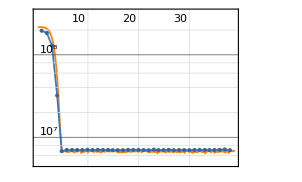
NetTrain Results
summary | ,,  batches:2214  rounds:39  time:1.4min  examples/s:21613
data | ,,  training examples:45000  validation examples:12680  processed examples:1771200  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:6.77×10^6
validation | ,,  loss:6.98×10^6
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{{11153.3,10788.,10716.,10766.8,11116.3,11535.6,12580.1,13398.4,13455.7,13345.3,13460.6,13397.,13189.5,13481.2,13331.1,13720.7,14221.4,14236.6,14295.1,14583.4,14470.4,13671.2,12882.6,11482.3,11488.6,11321.4,11271.6,11207.5,11164.,11698.8,12995.8,13763.7,13754.4,13510.9,13247.,12939.6,12614.5,12884.1,12956.,12960.6,12932.,13266.2,13733.8,14164.,14198.8,13421.4,12296.2,11899.4,10705.8,10468.1,10380.3,10531.2,10627.1,11465.3,12671.2,13836.5,14392.9,14611.7,14683.5,14466.1,14217.6,14286.4,14257.4,13977.2,13828.2,13922.9,14254.5,14587.8,14546.2,13792.7,12674.6,11331.6,10999.9,10580.5,10686.1,10691.,11017.1,11662.3,12920.1,13594.5,13446.1,13095.9,12998.,12600.5,12621.1,12295.,12006.9,12111.5,12547.2,12790.,13161.7,13563.6,13729.1,13157.1,12272.8,10844.2,10644.8,10416.7,10331.4,10293.2,10418.1,10582.8,11072.5,11415.3,11409.9,11212.7,11544.7,11421.4,11127.3,10943.5,10921.1,11212.6,11471.2,11843.1,12080.7,12310.4,12583.,12113.6,11619.8,10459.,10345.,10138.7,9974.8,9932.15,10032.1,10096.8,10207.8,10396.4,10389.7,10258.5,10086.7,9934.98,10064.6,9921.45,10062.6,10088.,10605.4,11306.1,12012.7,12558.7,12912.1,12194.5,11138.3,10615.9,9708.63,9427.22,9539.9,9401.41,9837.07,10915.3,12472.7,13060.3,12573.8,12064.3,11757.1,11567.4,11385.4,11316.4,11214.3,11295.3,11705.1,12385.,12968.1,13403.8,13650.,12796.6,11554.4,10426.6,10063.1,9824.85,9864.55,9916.92,10117.4,10789.9,12278.6,12852.,12471.7,11989.8,11678.8,11511.,11469.9,11578.1,11360.4,11602.2,12057.4,12707.5,13123.3,13559.1,13618.6,12733.,11487.9,10945.3,10279.5,10095.3,9909.73,9899.26,10199.,10902.9,12066.2,13005.5,13382.1,13481.2,13501.,13539.7,13578.7,13675.,13626.8,13611.6,13800.5,14095.2,14169.6,14193.3,13908.2,13008.9,11969.1,10679.5,10206.5,9757.04,9706.85,9675.74,9821.05,10427.6,12011.,13099.3,13361.9,13223.,12912.9,12598.5,12341.8,12478.2,12653.,12557.8,12532.7,12686.9,13026.2,13304.8,13536.9,12810.6,11619.5,10585.2,10285.,9906.9,9964.56,9834.97,9882.09,10335.1,11715.2,12426.9,12353.,12252.2,12683.8,13131.1,13199.,13305.4,13221.,13225.2,13285.8,13393.6,13420.4,13416.1,13244.2,12554.2,11577.7,10215.6,10105.4,9645.24,9584.17,9572.56,9673.84,9773.16,10310.6,10638.6,11063.6,11066.9,10774.3,10497.4,10282.5,10194.8,10183.8,10177.3,10654.8,11301.5,11705.3,11962.3,12254.9,11730.3,10925.4,10342.6,10077.4,9760.4,9778.76,9910.49,9970.55,10072.6,10188.7,10443.4,10772.9,11493.8,11865.9,11917.4,11712.8,11499.2,11228.6,11226.,11557.5,12101.5,12528.4,12828.6,12977.,12244.4,11193.1,10969.8,10021.8,9832.71,9718.01,9754.82,10089.4,11088.2,12181.3,13073.4,13203.6,13256.1,13317.2,13232.2,13051.1,13042.,13065.5,13078.2,13322.,13675.5,13863.9,14095.7,14126.6,13236.3,11991.9,10752.8,10781.5,10601.9,10437.,10427.2,10737.4,11478.5,12375.6,13017.7,12807.5,12685.,12591.8,12768.8,12799.9,12468.7,11512.3,11663.5,12059.5,12713.9,13131.7,13519.1,13717.9,12877.6,11698.9,11533.8,10354.1,10295.6,10349.4,10321.9,10589.9,10877.7,11645.,12352.3,12359.2,12296.1,12327.9,12405.1,12527.1,12823.8,13104.6,13503.8,14037.7,14458.8,14593.2,14738.4,14958.4,14082.1,12678.5,12373.5,10908.6,10479.8,10230.8,10272.2,10244.2,10808.1,12216.,13219.5,13468.4,13296.1,13792.,14358.,14879.6,15341.,15545.5,15678.7,15824.7,15887.1,15866.3,15976.,15845.4,14985.9,13590.2,12151.6,11666.,11170.5,11171.7,11308.6,11542.1,11841.9,13053.5,13887.8,14321.4,14530.2,14658.,14797.4,14789.3,14604.8,14801.6,15176.8,15492.5,15476.8,15327.5,15333.5,15354.,14551.1,13248.6,10709.6,11076.6,10609.6,10299.2,10259.6,10205.8,10317.6,10660.1,11202.6,11185.3,11213.6,11118.3,11057.1,10886.1,11202.1,11072.6,11268.,11848.1,12332.4,12526.2,12611.,12837.6,12304.9,11400.4,10495.5,10458.3,10234.5,10045.5,9903.12,9898.49,9791.39,10065.1,10487.5,11094.7,11537.5,11788.9,11921.4,12019.2,11964.6,11984.1,12038.3,12264.7,12649.5,12836.3,12872.3,12822.2,12047.5,11124.5,10689.4,9875.96,9469.69,9558.48,9565.48,9869.08,10483.,11403.3,12235.6,12250.5,12137.7,12040.8,12068.5,12044.2,12125.6,12154.5,12310.8,12604.6,13061.3,13392.3,13509.1,13703.5,12882.,11678.1,10716.9,10163.2,9737.05,9576.85,9753.07,9770.58,10399.4,11679.5,12271.2,12148.4,11923.6,11892.6,11940.7,12019.3,12233.8,12312.3,12464.6,12832.7,13358.4,13615.7,13693.6,13890.4,13068.6,11722.7,10983.5,10492.4,10095.8,10194.4,10302.9,10313.6,10547.1,11716.9,12222.8,12171.1,12072.1,12088.,12163.6,12222.1,12431.,12544.,12872.1,13200.2,13517.3,13684.9,13722.5,13919.4,13111.4,11875.8,10915.3,10297.8,10028.7,9849.37,9810.17,10073.4,10794.5,11844.3,12542.1,12642.,12438.1,12169.3,12124.4,12240.3,12553.6,12799.9,12989.2,13061.1,13293.4,13469.,13599.3,13798.8,13079.8,11869.3,10822.7,10120.8,9959.01,9975.59,9857.81,9908.91,10574.4,11519.4,12297.,12329.8,12267.3,12194.1,11879.5,11625.5,11688.9,11729.1,11963.8,12418.1,12790.7,12855.,12871.1,13074.8,12512.7,11501.1,10451.8,10101.1,9697.28,9427.68,9330.63,9400.91,9647.36,10143.2,10914.3,11297.7,11769.6,12048.4,12087.7,12031.3,12002.8,12064.5,11920.6,12057.2,12336.3,12419.5,12441.3,12464.7,11977.3,11114.1,10347.2,10007.6,9874.95,9635.39,9531.37,9574.07,9736.73,10098.,10696.4,11156.8,11321.1,11152.4,10998.7,10682.9,10513.9,10390.1,10218.4,10595.7,11216.4,11812.7,12200.8,12577.4,12048.7,11168.8,10645.2,9846.54,9471.33,9536.96,9609.98,9626.69,10189.9,11525.6,12591.5,12739.3,12692.4,12688.9,12566.8,12198.4,12233.2,12305.5,12566.7,12754.2,13384.1,13739.6,13837.7,14019.8,13243.1,11877.7,10867.6,9943.78,9695.9,9453.84,9643.71,9855.39,10504.2,11873.3,12753.8,13117.6,13260.3,13366.4,13458.1,13603.8,13868.7,14160.4,15048.5,15791.5,15638.7,15270.1,14722.8,14295.7,13403.7,12061.1,10783.,10336.4,10121.7,10188.3,10234.3,10441.3,10684.5,11949.6,12376.2,12305.8,12282.5,12286.7,12227.6,12352.9,12600.7,12719.4,12838.1,13022.9,13256.8,13393.3,13490.6,13605.8,12849.4,11614.,11149.1,10203.5,9847.11,9635.03,10007.2,10138.,10527.,11706.6,12677.1,13030.8,13192.1,13152.6,13247.7,13144.4,13082.4,13012.1,13216.5,13569.9,13832.7,13925.1,14027.,14226.8,13550.5,12228.4,10596.8,10707.1,10384.9,10390.7,10264.8,10321.7,10495.2,11303.,12152.3,12273.6,12150.3,11967.9,11903.2,11785.5,11767.3,11828.3,12009.3,12188.1,12293.5,12439.5,12565.8,12812.4,12356.9,11400.,10239.8,9755.42,9440.17,9426.76,9354.47,9466.94,9736.97,10202.1,10468.3,10815.9,11290.,11671.1,11861.9,11947.1,11997.6,11947.5,12017.5,12238.3,12519.1,12565.3,12553.,12514.1,11995.4,11156.8,10666.1,9680.31,9521.66,9732.64,9885.9,9942.19,9951.61,10194.,10611.9,11306.4,11751.2,11972.,11973.5,12347.7,12285.9,12384.6,12556.8,12926.9,13426.1,13628.1,13618.8,13726.2,13118.2,11868.8,11036.2,10072.2,10010.7,10131.1,10043.6,9987.47,10739.7,11730.3,12201.7,12236.8,12206.7,12266.2,12368.8,12432.3,12660.2,12847.7,13135.3,13639.6,14272.5,14572.3,14472.,14479.5,13683.8,12279.2,10681.2,10242.8,9804.7,9524.92,9426.32,9673.15,10159.6,11407.1,12498.9,12974.1,13275.3,13565.4,13648.1,13733.3,13820.4,13678.4,13647.8,13813.,14008.,13973.1,13856.1,13704.9,12892.9,11630.4,11456.6,10287.4,10123.5,9936.94,9880.62,10145.,10447.1,11577.9,12566.9,12652.2,12654.7,12776.7,12849.4,13018.9,13188.4,13537.7,13981.8,14506.,14997.8,15169.7,15127.8,15136.9,14330.1,12868.9,11291.4,10718.4,10367.9,10298.6,10203.6,10398.9,10585.4,11664.1,12578.3,12743.2,12648.1,12575.8,12593.4,12625.2,12815.9,12944.7,13284.7,13782.3,14258.9,14414.5,14331.6,14299.7,13656.4,12270.5,12422.5,10908.8,10656.2,10362.1,10266.,10496.,10688.8,11867.4,12906.4,13052.2,12929.9,13277.,13876.7,14077.2,14270.1,14627.7,15078.5,15564.2,15875.4,15825.,15506.7,15460.8,14879.9,13695.9,12495.8,11413.3,10739.1,10535.3,10678.9,10656.5,10728.1,11207.6,11777.6,12468.4,13245.5,13927.4,14312.5,14545.2,14846.9,15195.4,15451.9,15832.9,16069.5,15924.9,15545.7,15424.2,14806.4,13709.8,10521.2,11527.3,10847.8,10409.6,10277.3,10099.,10108.5,10551.2,11004.5,11295.3,11676.5,11967.4,12070.6,12084.5,11988.,11846.7,11707.3,12105.,12343.7,12168.9,12159.6,12154.4,11687.1,10932.4,10370.7,9934.55,9780.6,9543.58,9740.34,9827.32,10050.5,10111.2,10506.9,10805.6,11437.5,11854.3,11767.,11657.6,11644.4,11468.3,11361.9}}]

```mathematica
trainednet[rsample[[2,1]]]
```

```mathematica
sobj=NetStateObject[trainednet]
```

NetStateObject::arg1: First argument to NetStateObject should be a valid net.

$Failed

```mathematica
tvalues=Table[trainednet[testdata[[i,1]]],{i,1,Length@testdata}]
```

{1}
 |  |  |  |

```mathematica
results=Union@Flatten@NestList[Drop[Join[#,{trainednet[#]}],1]&,testdata[[1,1]],100]
```

{9915.12,1095}
 |  |  |  |

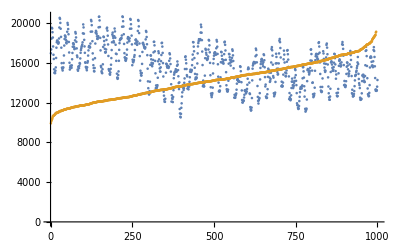

```mathematica
ListPlot[{testdata[[1;;1000,2]],results}]
```